# Notebook 2: Dynamics of strategy competition Author: Mari Kawakatsu (marikawa@sas.upenn.edu)

## Part 1: Competition among ALLC, ALLD, and pDISC

### Code for plotting

```mathematica
Clear["Global`*"];
up = .02;
ua = .02;
eps := (1 - ua)(1 - up) + ua up;
nu1 = 0.5;
nu2 := 1.0 - nu1;

setupallequations[p_,q_,Atype_,Btype_]:=(

Clear[f1X,f1Y,f1Z,f2X,f2Y,f2Z];
Clear[A11,A12,B11,B12,A21,A22,B21,B22];
Clear[pgoodGC,pgoodGD,pgoodBC,pgoodBD];
Clear[g11,g12,g21,g22,gbul1,gbul2,gstar1,gstar2,g11a1,g11b1,g11c1,g11d1,g12a1,g12b1,g12c1,g12d1,g21a1,g21b1,g21c1,g21d1,g22a1,g22b1,g22c1,g22d1,g11a2,g11b2,g11c2,g11d2,g12a2,g12b2,g12c2,g12d2,g21a2,g21b2,g21c2,g21d2,g22a2,g22b2,g22c2,g22d2,g11a3,g11b3,g11c3,g11d3,g12a3,g12b3,g12c3,g12d3,g21a3,g21b3,g21c3,g21d3,g22a3,g22b3,g22c3,g22d3,g11a4,g11b4,g11c4,g11d4,g12a4,g12b4,g12c4,g12d4,g21a4,g21b4,g21c4,g21d4,g22a4,g22b4,g22c4,g22d4];

A11 = KroneckerDelta[Atype, 1] + KroneckerDelta[Atype, 2];
A12 = KroneckerDelta[Atype, 2];
B11 = KroneckerDelta[Btype, 1] + KroneckerDelta[Btype, 2];
B12 = KroneckerDelta[Btype, 2];
A21 = A12;
A22 = A11;
B21 = B12;
B22 = B11;

(* observer view - donor intent - probgood *)
pgoodGC=eps;
pgoodGD=ua;
pgoodBC=p(eps-ua)+q(1-eps-ua)+ua;
pgoodBD=q(1-2ua)+ua;

(* generation equations for reputation relations *)
g11=f1X g11X+f1Y g11Y+f1Z g11Z;
g12=f1X g12X+f1Y g12Y+f1Z g12Z;
g21=f2X g21X+f2Y g21Y+f2Z g21Z;
g22=f2X g22X+f2Y g22Y+f2Z g22Z;

gbul1 = nu1 g11 + nu2 g21;
gbul2 = nu1 g12 + nu2 g22;
gstar1 = nu1 g11S + nu2 g21S;
gstar2 = nu1 g12S + nu2 g22S;

g11a1 = nu1 (f1X g11X g11X+f1Y g11Y g11Y+f1Z g11Z g11Z)+ nu2 (f2X g21X g21X+f2Y g21Y g21Y+f2Z g21Z g21Z);
g11b1 = gbul1 - g11a1;
g11c1 = gbul1 - g11a1;
g11d1 = 1 - gbul1 - gbul1 + g11a1;
g12a1 = nu1(f1X g12X g11X+f1Y g12Y g11Y+f1Z g12Z g11Z)+nu2(f2X g22X g21X+f2Y g22Y g21Y+f2Z g22Z g21Z);
g12b1 = gbul2 - g12a1;
g12c1 = gbul1 - g12a1;
g12d1 = 1 - gbul2 - gbul1 + g12a1;
g21a1 = nu1(f1X g11X g12X+f1Y g11Y g12Y+f1Z g11Z g12Z)+nu2(f2X g21X g22X+f2Y g21Y g22Y+f2Z g21Z g22Z);
g21b1 = gbul1 - g21a1;
g21c1 = gbul2 - g21a1;
g21d1 = 1 - gbul1 - gbul2 + g21a1;
g22a1 = nu1(f1X g12X g12X+f1Y g12Y g12Y+f1Z g12Z g12Z)+nu2(f2X g22X g22X+f2Y g22Y g22Y+f2Z g22Z g22Z);
g22b1 = gbul2 - g22a1;
g22c1 = gbul2 - g22a1;
g22d1 = 1 - gbul2 - gbul2 + g22a1;
g11a2 = nu1 g11S g11 + nu2 g21S g21;
g11b2 = gbul1 - g11a2;
g11c2 = gstar1 - g11a2;
g11d2 = 1 - gbul1 - gstar1 + g11a2;
g12a2 = nu1 g12S g11 + nu2 g22S g21;
g12b2 = gbul2 - g12a2;
g12c2 = gstar1 - g12a2;
g12d2 = 1 - gbul2 - gstar1 + g12a2;
g21a2 = nu1 g11S g12+ nu2 g21S g22;
g21b2 = gbul1 - g21a2;
g21c2 = gstar2 - g21a2;
g21d2 = 1 - gbul1 - gstar2 + g21a2;
g22a2 = nu1 g12S g12+ nu2 g22S g22;
g22b2 = gbul2 - g22a2;
g22c2 = gstar2 - g22a2;
g22d2 = 1 - gbul2 - gstar2 + g22a2;
g11a3 = nu1 g11 g11S + nu2 g21 g21S;
g11b3 = gstar1 - g11a3;
g11c3 = gbul1 - g11a3;
g11d3 = 1 - gstar1 - gbul1 + g11a3;
g12a3 = nu1 g12 g11S + nu2 g22 g21S;
g12b3 = gstar2 - g12a3;
g12c3 = gbul1 - g12a3;
g12d3 = 1 - gstar2 - gbul1 + g12a3;
g21a3 = nu1 g11 g12S + nu2 g21 g22S;
g21b3 = gstar1 - g21a3;
g21c3 = gbul2 - g21a3;
g21d3 = 1 - gstar1 - gbul2 + g21a3;
g22a3 = nu1 g12 g12S + nu2 g22 g22S;
g22b3 = gstar2 - g22a3;
g22c3 = gbul2 - g22a3;
g22d3 = 1 - gstar2 - gbul2 + g22a3;
g11a4 = nu1 g11S g11S + nu2 g21S g21S;
g11b4 = gstar1 - g11a4;
g11c4 = gstar1 - g11a4;
g11d4 = 1 - gstar1 - gstar1 + g11a4;
g12a4 = nu1 g12S g11S + nu2 g22S g21S;
g12b4 = gstar2 - g12a4;
g12c4 = gstar1 - g12a4;
g12d4 = 1 - gstar2 - gstar1 + g12a4;
g21a4 = nu1 g11S g12S + nu2 g21S g22S;
g21b4 = gstar1 - g21a4;
g21c4 = gstar2 - g21a4;
g21d4 = 1 - gstar1 - gstar2 + g21a4;
g22a4 = nu1 g12S g12S + nu2 g22S g22S;
g22b4 = gstar2 - g22a4;
g22c4 = gstar2 - g22a4;
g22d4 = 1 - gstar2 - gstar2 + g22a4;
)

nsoln[rr_,uaa_,upp_,fXXX_, fYYY_, fZZZ_]:=(
Clear[f1X,f1Y,f1Z,f2X,f2Y,f2Z];
f1X = fXXX;
f1Y = fYYY;
f1Z = fZZZ;
f2X = fXXX;
f2Y = fYYY;
f2Z = fZZZ;
FindRoot[{
g11X ==  gbul1 pgoodGC + (1 - gbul1) pgoodBC,
g12X ==  gbul2 pgoodGC + (1 - gbul2) pgoodBC,
g21X ==  gbul1 pgoodGC + (1 - gbul1) pgoodBC,
g22X ==  gbul2 pgoodGC + (1 - gbul2) pgoodBC,
g11Y ==  gbul1 pgoodGD + (1 - gbul1) pgoodBD,
g12Y ==  gbul2 pgoodGD + (1 - gbul2) pgoodBD,
g21Y ==  gbul1 pgoodGD + (1 - gbul1) pgoodBD,
g22Y ==  gbul2 pgoodGD + (1 - gbul2) pgoodBD,
g11Z == (1 - rr)((1 - A11)(g11a1 pgoodGC + g11b1 pgoodGD + g11c1 pgoodBC + g11d1 pgoodBD)+ A11 (gbul1 pgoodGC + (1 - gbul1) pgoodBD))+ rr (g11a2 pgoodGC + g11b2 pgoodGD + g11c2 pgoodBC + g11d2 pgoodBD),
g12Z == (1 - rr)((1 - A21)(g12a1 pgoodGC + g12b1 pgoodGD + g12c1 pgoodBC + g12d1 pgoodBD)+ A21 (gbul2 pgoodGC + (1 - gbul2) pgoodBD))+ rr (g12a2 pgoodGC + g12b2 pgoodGD + g12c2 pgoodBC + g12d2 pgoodBD),
g21Z == (1 -rr)((1 - A12)(g21a1 pgoodGC + g21b1 pgoodGD + g21c1 pgoodBC + g21d1 pgoodBD)+ A12 (gbul1 pgoodGC + (1 - gbul1) pgoodBD))+ rr (g21a2 pgoodGC + g21b2 pgoodGD + g21c2 pgoodBC + g21d2 pgoodBD),
g22Z == (1 - rr)((1 - A22)(g22a1 pgoodGC + g22b1 pgoodGD + g22c1 pgoodBC + g22d1 pgoodBD)+ A22 (gbul2 pgoodGC + (1 - gbul2) pgoodBD))+ rr (g22a2 pgoodGC + g22b2 pgoodGD + g22c2 pgoodBC + g22d2 pgoodBD),
g11S == f1X(gstar1 pgoodGC + (1 - gstar1) pgoodBC)+ f1Y (gstar1 pgoodGD + (1 - gstar1) pgoodBD)+f1Z( (1 - rr)(g11a3 pgoodGC + g11b3 pgoodGD + g11c3 pgoodBC + g11d3 pgoodBD)+ rr ((1 - B11)(g11a4 pgoodGC + g11b4 pgoodGD + g11c4 pgoodBC + g11d4 pgoodBD)+ B11 (gstar1 pgoodGC + (1 - gstar1) pgoodBD))),
g12S == f1X(gstar2 pgoodGC + (1 - gstar2) pgoodBC)+ f1Y (gstar2 pgoodGD + (1 - gstar2) pgoodBD)+f1Z((1 - rr)(g12a3 pgoodGC + g12b3 pgoodGD + g12c3 pgoodBC + g12d3 pgoodBD)+ rr ((1 - B21)(g12a4 pgoodGC + g12b4 pgoodGD + g12c4 pgoodBC + g12d4 pgoodBD)+ B21 (gstar2 pgoodGC + (1 - gstar2) pgoodBD))),
g21S == f2X(gstar1 pgoodGC + (1 - gstar1) pgoodBC)+ f2Y (gstar1 pgoodGD + (1 - gstar1) pgoodBD)+f2Z((1 - rr)(g21a3 pgoodGC + g21b3 pgoodGD + g21c3 pgoodBC + g21d3 pgoodBD)+ rr ((1 - B12)(g21a4 pgoodGC + g21b4 pgoodGD + g21c4 pgoodBC + g21d4 pgoodBD)+ B12 (gstar1 pgoodGC + (1 - gstar1) pgoodBD))),
g22S == f2X(gstar2 pgoodGC + (1 - gstar2) pgoodBC)+ f2Y (gstar2 pgoodGD + (1 - gstar2) pgoodBD)+f2Z( (1 - rr)(g22a3 pgoodGC + g22b3 pgoodGD + g22c3 pgoodBC + g22d3 pgoodBD)+ rr ((1 - B22)(g22a4 pgoodGC + g22b4 pgoodGD + g22c4 pgoodBC + g22d4 pgoodBD)+ B22 (gstar2 pgoodGC + (1 - gstar2) pgoodBD)))}
 /.{ ua->uaa, up->upp},{{g11X,.49},{g12X,.49},{g21X,.49},{g22X,.49},
{g11Y,.49},{g12Y,.49},{g21Y,.49},{g22Y,.49},{g11Z,.49},{g12Z,.49},{g21Z,.49},{g22Z,.49},
{g11S,.9},{g12S,.9},{g21S,.9},{g22S,.9}
}
]
)

fsoln[fXX_, fYY_,b_,c_,r_,alpha_] :=Module[{fZZ,repsoln,f1X,f1Y,f1Z,f2X,f2Y,f2Z,pi1X,pi2X,pi1Y,pi2Y,pi1Z,pi2Z,pi,piX,piY,piZ,fXdot,fYdot,fZdot}, 
Clear[fZZ,f1X,f1Y,f1Z,f2X,f2Y,f2Z,pi1X,pi2X,pi1Y,pi2Y,pi1Z,pi2Z,pi,piX,piY,piZ,fXdot,fYdot,fZdot];
fZZ = 1 - fXX - fYY;
repsoln = nsoln[r,ua, up,fXX, fYY, fZZ];
f1X = fXX;
f1Y = fYY;
f1Z = fZZ;
f2X = fXX;
f2Y = fYY;
f2Z = fZZ;
pi1X=(1-up)(b (nu1(f1X+f1Z ((1-r)g11X + r g11S))+nu2(f2X + f2Z ((1-r)g12X + r g12S))) - c)/.repsoln;
pi2X=(1-up)(b (nu1(f1X+f1Z ((1-r)g21X + r g21S))+nu2(f2X + f2Z ((1-r)g22X + r g22S))) - c)/.repsoln;
pi1Y=(1-up)(b (nu1(f1X+f1Z ((1-r)g11Y + r g11S))+nu2(f2X + f2Z ((1-r)g12Y + r g12S))))/.repsoln;
pi2Y=(1-up)(b (nu1(f1X+f1Z ((1-r)g21Y + r g21S))+nu2(f2X + f2Z ((1-r)g22Y + r g22S))))/.repsoln;
pi1Z=(1-up)(b (nu1(f1X+f1Z ((1-r)g11Z + r g11S))+nu2(f2X + f2Z ((1-r)g12Z + r g12S))) - c((1-r) gbul1 + r gstar1))-alpha(1-r)/.repsoln(*fixed*);
pi2Z=(1-up)(b (nu1(f1X+f1Z ((1-r)g21Z + r g21S))+nu2(f2X + f2Z ((1-r)g22Z + r g22S))) - c((1-r) gbul2 + r gstar2))-alpha(1-r)/.repsoln(*fixed*);
pi=nu1(f1X pi1X+f1Y pi1Y+f1Z pi1Z) + nu2 (f2X pi2X+f2Y pi2Y+f2Z pi2Z);

piX = nu1 pi1X + nu2 pi2X;
piY = nu1 pi1Y + nu2 pi2Y;
piZ = nu1 pi1Z + nu2 pi2Z;

fXdot =fXX (piX-pi);
fYdot =fYY (piY-pi);
fZdot =fZZ (piZ-pi);

{fXdot, fYdot, fZdot}
]

(*plot theme*)
Themes`AddThemeRules["theme_mk"
,RegionFillingStyle->None
,RegionBoundaryStyle->Directive[Thin,Gray](*{Black,Thickness[0.001]}, *)
,StreamColorFunction->None
,StreamStyle->RGBColor["#1874CD"](*Gray*)
,Evaluated -> True
,StreamScale->{Medium,Automatic,Scaled[0.35]}
];
$PlotTheme="theme_mk";
directory=NotebookDirectory[]<>"plots/";

MakeTernaryPlot2[b_,c_,r_,Atype_,Btype_,p_,q_,alpha_] := (

Print["processing stereo propensity (p) = ",r,", rep cost (η) = ",alpha];

setupallequations[p,q, Atype,Btype];

fvals[fX_,fY_] := fsoln[fX,fY,b,c,r,alpha];

dotfX[fX_?NumericQ,fY_?NumericQ]:=fvals[fX,fY][[1]];
dotfY[fX_?NumericQ,fY_?NumericQ]:=fvals[fX,fY][[2]];
dotfZ[fX_?NumericQ,fY_?NumericQ]:=fvals[fX,fY][[3]];

vX:=dotfX[fX,fY];
vY:=dotfY[fX,fY];

(*equilibria*)
eqColor=RGBColor["#ff8c00"];
eqThresh=10^-8;

Off[FindRoot::reged];
eqZ={{fX->0.,fY->0.},If[r==0.0&&alpha<0.15,True,If[(Atype==2&&alpha<r*1.05&&9*r<b)∨(Atype==1&&alpha<r*0.3&&9*r<b),True,False]],"A"} (* stable if alpha below some value; change threshold to make sure color is correct *);
eqY={{fX->0.,fY->1.},True,"A"};
eqX={{fX->1.,fY->0.},False,"A"};
eqYZ1cand=FindRoot[{vX==0,vY==0},{{fX,0.10,0.,0.2},{fY,0.70-alpha*0.3,0.,1.}}];
eqYZ1={eqYZ1cand,If[Abs[1-fX/.eqYZ1cand]<eqThresh,False,If[Abs[1-fY/.eqYZ1cand]<eqThresh,True,If[Abs[fX+fY/.eqYZ1cand]<eqThresh,eqZ[[2]],False]]],"B"};
eqYZ2cand=FindRoot[{vX==0,vY==0},{{fX,0.15,0.,0.2},{fY,0.60,0.,1.}}];
eqYZ2={eqYZ2cand,If[Abs[1-fX/.eqYZ2cand]<eqThresh,False,If[Abs[1-fY/.eqYZ2cand]<eqThresh,True,If[Abs[fX+fY/.eqYZ2cand]<eqThresh,eqZ[[2]],False]]],"B"};
eqYZ3cand=FindRoot[{vX==0,vY==0},{{fX,0.15,0.,0.2},{fY,0.40,0.,1.}}];
eqYZ3={eqYZ3cand,If[Abs[1-fX/.eqYZ3cand]<eqThresh,False,If[Abs[1-fY/.eqYZ3cand]<eqThresh,True,If[Abs[fX+fY/.eqYZ3cand]<eqThresh,eqZ[[2]],False]]],"B"};
eqYZ4cand=FindRoot[{vX==0,vY==0},{{fX,0.01,0.,0.2},{fY,0.55,0.,1.}}];
eqYZ4={eqYZ4cand,If[Abs[1-fX/.eqYZ4cand]<eqThresh,False,If[Abs[1-fY/.eqYZ4cand]<eqThresh,True,If[Abs[fX+fY/.eqYZ4cand]<eqThresh,eqZ[[2]],False]]],"B"};
eqYZ5cand=FindRoot[{vX==0,vY==0},{{fX,0.01,0.,0.2},{fY,0.2,0.,1.}}];
eqYZ5={eqYZ5cand,If[Abs[1-fX/.eqYZ5cand]<eqThresh,False,If[Abs[1-fY/.eqYZ5cand]<eqThresh,True,If[Abs[fX+fY/.eqYZ5cand]<eqThresh,eqZ[[2]],False]]],"B"};
eqXZcand=FindRoot[{vX==0,vY==0},{{fX,0.6,0.,1.},{fY,0.1,0.,0.2}}];
eqXZ={eqXZcand,If[Abs[1-fY/.eqXZcand]<eqThresh,True,If[Abs[1-fX/.eqXZcand]<eqThresh,False,If[Abs[fX+fY/.eqXZcand]<eqThresh,eqZ[[2]],If[Abs[fY/.eqXZcand]<eqThresh&&(fX/.eqXZcand)<0.75,True,False]]]],"C"};
eqXYZ1={FindRoot[{vX==0,vY==0},{{fX,0.15,0.02,0.98},{fY,0.65,0.02,0.98}}],False,"D"};
eqXYZ2={FindRoot[{vX==0,vY==0},{{fX,0.65,0.02,0.98},{fY,0.15,0.02,0.98}}],False,"D"};
eqXYZ3={FindRoot[{vX==0,vY==0},{{fX,0.40,0.02,0.98},{fY,0.15,0.02,0.98}}],False,"D"};

eqs=Select[{eqY,eqX,eqZ,eqYZ1,eqYZ2,eqYZ3,eqYZ4,eqYZ5,eqXZ,eqXYZ1,eqXYZ2,eqXYZ3},0<=(fX+fY/.#[[1]])<=1&&(Chop[({vX,vY}/.#[[1]]),eqThresh]=={0.,0.})(*&&(#≠{{fX->0.,fY->1.},False,"D"})*)&];
eqs=Union[eqs,SameTest->(Abs[(fX/.#[[1]])-(fX/.#2[[1]])]<eqThresh&&Abs[(fY/.#[[1]])-(fY/.#2[[1]])]<eqThresh&)](* delete duplicates *);

(*Print[eqs];*)
(*Print[({vX,vY}/.#[[1]])&/@eqs];*)

TernCoords[x_,y_]={{1/2,-1/2},{-Tan[Pi/3]/2,-Tan[Pi/3]/2}}.{x,y}+{1/2,Tan[Pi/3]/2};
diskradius=.02;
textoffset=.075;
thickness=.0075;

types={"private","group-wise","public"};
typelabel[Ai_,Bi_]:=StringJoin[ToString[Style[types[[Ai+1]],Bold],StandardForm]," reputations, ",ToString[Style[types[[Bi+1]],Bold],StandardForm]," stereotypes"];
paramlabel[rr_,aalpha_]:="p ="<>ToString[PaddedForm[r,{2,2}]]<>", η ="<>ToString[PaddedForm[alpha,{2,2}]];

vlabels={
Graphics[Text[Style["ALLD",16],{-textoffset,-textoffset}]],
Graphics[Text[Style["ALLC",16],{1+textoffset,-textoffset}]],
Graphics[Text[Style[ToString[r]<>"DISC",16],{1/2,Tan[Pi/3]/2+textoffset}]],
Graphics[Text[Style[typelabel[Atype,Btype],13],{1/2,Tan[Pi/3]/2+textoffset*5}]],
Graphics[Text[Style[paramlabel[r,alpha],16],{1/2,Tan[Pi/3]/2+textoffset*3}]]
};

(* new format *)
streampoints=DeleteCases[Flatten[Table[If[0≤fX0+fY0≤1,{fX0,fY0},{}],{fX0,Subdivide[1.,20][[;;]]},{fY0,Subdivide[1.,20][[;;]]}],1],{}];

dp=StreamPlot[{vX,vY},{fX,0,1},{fY,0,1},RegionFunction->(#1≤1-#2&),StreamPoints->(*None*)streampoints,StreamScale->{Medium,Automatic,Scaled[0.35]}];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];

(* show figure *)
eqdots=({EdgeForm[Directive[eqColor,Thickness[thickness]]],If[#[[2]],eqColor,White],Disk[TernCoords[fX,fY]/.#[[1]],diskradius]}&/@eqs);
stereotypes=Show[ternplot,vlabels, ImageSize->{250,250},PlotRangePadding->.05,Epilog->eqdots];

stereotypes

)
```

### Make grids with varying parameters

processing stereo propensity (p) = 0., rep cost (η) = 0.1

processing stereo propensity (p) = 0., rep cost (η) = 0.2

processing stereo propensity (p) = 0., rep cost (η) = 0.3

processing stereo propensity (p) = 0., rep cost (η) = 0.4

processing stereo propensity (p) = 0., rep cost (η) = 0.7

processing stereo propensity (p) = 0., rep cost (η) = 1.

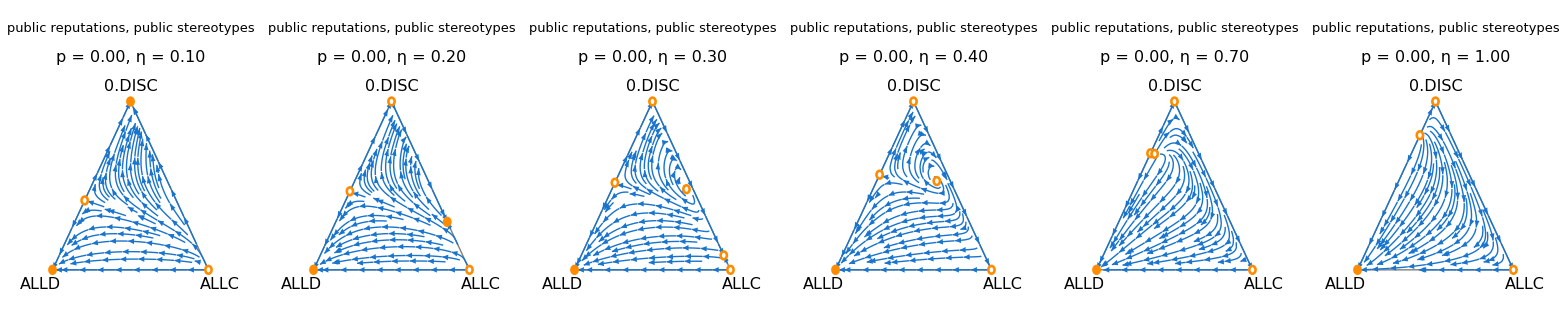

FigS12.pdf

```mathematica
(* vary access cost --- ZOOMED IN *)
AAA=2;BBB=2;bb=3;rr=0.;alphas={0.1,0.2,0.3,0.4,0.7,1.0};
stereotypes=Grid[Table[MakeTernaryPlot2[bb,1,rr,AAA,BBB,0,1,alpha],{dummy, {0.}},{alpha,alphas}]]

filename="FigS12.pdf"
Export[directory<>filename,stereotypes];
Beep[] (* this figure takes a while; Beep[] will let you know when it's done *)
```

processing stereo propensity (p) = 0., rep cost (η) = 0.1

processing stereo propensity (p) = 0.33, rep cost (η) = 0.1

processing stereo propensity (p) = 0.67, rep cost (η) = 0.1

processing stereo propensity (p) = 1., rep cost (η) = 0.1

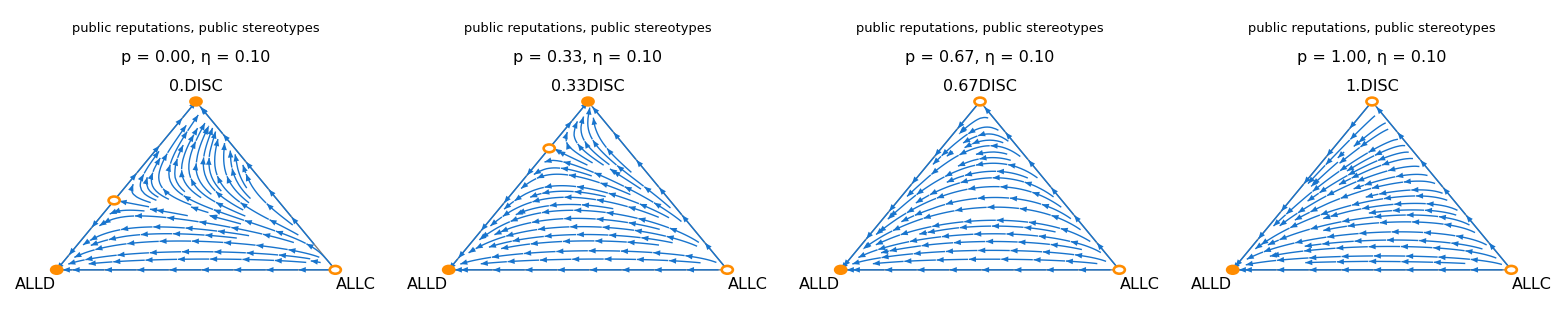

Fig4_A-D.pdf

```mathematica
(* vary stereotyping propensity, public/public *)
AAA=2;BBB=2;bb=3;aalpha=0.1;rs={0.,0.33,0.67,1.};
stereotypes=Grid[Table[MakeTernaryPlot2[bb,1,r,AAA,BBB,0,1,aalpha],{dummy, {0.}},{r,rs}]]

filename="Fig4_A-D.pdf"
Export[directory<>filename,stereotypes];
Beep[] (* this figure takes a while; Beep[] will let you know when it's done *)
```

processing stereo propensity (p) = 0., rep cost (η) = 0.1

processing stereo propensity (p) = 0.33, rep cost (η) = 0.1

processing stereo propensity (p) = 0.67, rep cost (η) = 0.1

processing stereo propensity (p) = 1., rep cost (η) = 0.1

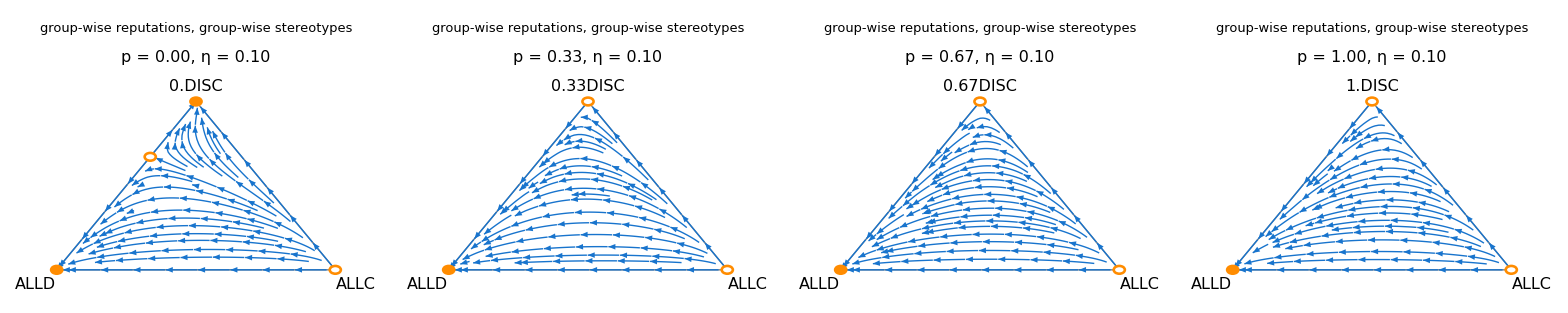

FigS11_A-D.pdf

```mathematica
(* vary stereotyping propensity, group-wise/group-wise *)
AAA=1;BBB=1;bb=3;aalpha=0.1;rs={0.,0.33,0.67,1.};
stereotypes=Grid[Table[MakeTernaryPlot2[bb,1,r,AAA,BBB,0,1,aalpha],{dummy, {0.}},{r,rs}]]

filename="FigS11_A-D.pdf"
Export[directory<>filename,stereotypes];
Beep[] (* this figure takes a while; Beep[] will let you know when it's done *)
```

## Part 2: Competition among ALLD, 0DISC, and pDISC

### Code for plotting

```mathematica
Clear["Global`*"];
up = .02;
ua = .02;
eps = (1 - ua)(1 - up) + ua up;
nu1 = 0.5;
nu2 := 1.0 - nu1;

setupallequations[p_,q_,Atype_,Btype_]:=(

Clear[f1X,f1Y,f1Z,f2X,f2Y,f2Z];
Clear[A11,A12,B11,B12,A21,A22,B21,B22];
Clear[pgoodGC,pgoodGD,pgoodBC,pgoodBD];
Clear[g11,g12,g21,g22,gbul1,gbul2,gstar1,gstar2,g11a1,g11b1,g11c1,g11d1,g12a1,g12b1,g12c1,g12d1,g21a1,g21b1,g21c1,g21d1,g22a1,g22b1,g22c1,g22d1,g11a2,g11b2,g11c2,g11d2,g12a2,g12b2,g12c2,g12d2,g21a2,g21b2,g21c2,g21d2,g22a2,g22b2,g22c2,g22d2,g11a3,g11b3,g11c3,g11d3,g12a3,g12b3,g12c3,g12d3,g21a3,g21b3,g21c3,g21d3,g22a3,g22b3,g22c3,g22d3,g11a4,g11b4,g11c4,g11d4,g12a4,g12b4,g12c4,g12d4,g21a4,g21b4,g21c4,g21d4,g22a4,g22b4,g22c4,g22d4];

A11 = KroneckerDelta[Atype, 1] + KroneckerDelta[Atype, 2];
A12 = KroneckerDelta[Atype, 2];
B11 = KroneckerDelta[Btype, 1] + KroneckerDelta[Btype, 2];
B12 = KroneckerDelta[Btype, 2];
A21 = A12;
A22 = A11;
B21 = B12;
B22 = B11;

(* observer view - donor intent - probgood *)
pgoodGC=eps;
pgoodGD=ua;
pgoodBC=p(eps-ua)+q(1-eps-ua)+ua;
pgoodBD=q(1-2ua)+ua;

(* generation equations for reputation relations *)
g11=f1Y g11Y+f1X g11X + f1Z g11Z;
g12=f1Y g12Y+f1X g12X + f1Z g12Z;
g21=f2Y g21Y+f2X g21X + f2Z g21Z;
g22=f2Y g22Y+f2X g22X + f2Z g22Z;

gbul1 = nu1 g11  + nu2 g21;
gbul2 = nu1 g12  + nu2 g22;
gstar1 = nu1 g11S  + nu2 g21S;
gstar2 = nu1 g12S  + nu2 g22S;

g11a1 = nu1 (f1Y g11Y g11Y+f1X g11X g11X +f1Z g11Z g11Z) + nu2(f2Y g21Y g21Y+f2X g21X g21X +f2Z g21Z g21Z);
g11b1 = gbul1 - g11a1;
g11c1 = gbul1 - g11a1;
g11d1 = 1 - gbul1 - gbul1 + g11a1;
g12a1 = nu1 (f1Y g12Y g11Y+f1X g12X g11X + f1Z g12Z g11Z)+ nu2 (f2Y g22Y g21Y+f2X g22X g21X +f2Z g22Z g21Z);
g12b1 = gbul2 - g12a1;
g12c1 = gbul1 - g12a1;
g12d1 = 1 - gbul2 - gbul1 + g12a1;
g21a1 = nu1(f1Y g11Y g12Y+f1X g11X g12X + f1Z g11Z g12Z)+ nu2 (f2Y g21Y g22Y+f2X g21X g22X +f2Z g21Z g22Z);
g21b1 = gbul1 - g21a1;
g21c1 = gbul2 - g21a1;
g21d1 = 1 - gbul1 - gbul2 + g21a1;
g22a1 = nu1(f1Y g12Y g12Y+f1X g12X g12X + f1Z g12Z g12Z)+ nu2 (f2Y g22Y g22Y+f2X g22X g22X +f2Z g22Z g22Z);
g22b1 = gbul2 - g22a1;
g22c1 = gbul2 - g22a1;
g22d1 = 1 - gbul2 - gbul2 + g22a1;
g11a2 = nu1 g11S g11 + nu2 g21S g21;
g11b2 = gbul1 - g11a2;
g11c2 = gstar1 - g11a2;
g11d2 = 1 - gbul1 - gstar1 + g11a2;
g12a2 = nu1 g12S g11 + nu2 g22S g21;
g12b2 = gbul2 - g12a2;
g12c2 = gstar1 - g12a2;
g12d2 = 1 - gbul2 - gstar1 + g12a2;
g21a2 = nu1 g11S g12 + nu2 g21S g22;
g21b2 = gbul1 - g21a2;
g21c2 = gstar2 - g21a2;
g21d2 = 1 - gbul1 - gstar2 + g21a2;
g22a2 = nu1 g12S g12 + nu2 g22S g22;
g22b2 = gbul2 - g22a2;
g22c2 = gstar2 - g22a2;
g22d2 = 1 - gbul2 - gstar2 + g22a2;
g11a3 = nu1 g11 g11S + nu2 g21 g21S;
g11b3 = gstar1 - g11a3;
g11c3 = gbul1 - g11a3;
g11d3 = 1 - gstar1 - gbul1 + g11a3;
g12a3 = nu1 g12 g11S + nu2 g22 g21S;
g12b3 = gstar2 - g12a3;
g12c3 = gbul1 - g12a3;
g12d3 = 1 - gstar2 - gbul1 + g12a3;
g21a3 = nu1 g11 g12S + nu2 g21 g22S;
g21b3 = gstar1 - g21a3;
g21c3 = gbul2 - g21a3;
g21d3 = 1 - gstar1 - gbul2 + g21a3;
g22a3 = nu1 g12 g12S + nu2 g22 g22S;
g22b3 = gstar2 - g22a3;
g22c3 = gbul2 - g22a3;
g22d3 = 1 - gstar2 - gbul2 + g22a3;
g11a4 = nu1 g11S g11S + nu2 g21S g21S;
g11b4 = gstar1 - g11a4;
g11c4 = gstar1 - g11a4;
g11d4 = 1 - gstar1 - gstar1 + g11a4;
g12a4 = nu1 g12S g11S + nu2 g22S g21S;
g12b4 = gstar2 - g12a4;
g12c4 = gstar1 - g12a4;
g12d4 = 1 - gstar2 - gstar1 + g12a4;
g21a4 = nu1 g11S g12S + nu2 g21S g22S;
g21b4 = gstar1 - g21a4;
g21c4 = gstar2 - g21a4;
g21d4 = 1 - gstar1 - gstar2 + g21a4;
g22a4 = nu1 g12S g12S + nu2 g22S g22S;
g22b4 = gstar2 - g22a4;
g22c4 = gstar2 - g22a4;
g22d4 = 1 - gstar2 - gstar2 + g22a4;
)

nsoln[rr1_,rr2_,uaa_,upp_,fX_,fY_,fZ_]:=(
Clear[f1X,f1Y,f1Z,f2X,f2Y,f2Z];
f1Y=fY;
f1X=fX;
f1Z=fZ;
f2Y=fY;
f2X=fX;
f2Z=fZ;
FindRoot[{
g11Y ==  gbul1 pgoodGD + (1 - gbul1) pgoodBD,
g12Y ==  gbul2 pgoodGD + (1 - gbul2) pgoodBD,
g21Y ==  gbul1 pgoodGD + (1 - gbul1) pgoodBD,
g22Y ==  gbul2 pgoodGD + (1 - gbul2) pgoodBD,
g11X == (1-rr1)((1 - A11)(g11a1 pgoodGC + g11b1 pgoodGD + g11c1 pgoodBC + g11d1 pgoodBD)+ A11 (gbul1 pgoodGC + (1 - gbul1) pgoodBD))+ rr1 (g11a2 pgoodGC + g11b2 pgoodGD + g11c2 pgoodBC + g11d2 pgoodBD),
g12X == (1-rr1)((1 - A21)(g12a1 pgoodGC + g12b1 pgoodGD + g12c1 pgoodBC + g12d1 pgoodBD)+ A21 (gbul2 pgoodGC + (1 - gbul2) pgoodBD))+ rr1 (g12a2 pgoodGC + g12b2 pgoodGD + g12c2 pgoodBC + g12d2 pgoodBD),
g21X == (1-rr1)((1 - A12)(g21a1 pgoodGC + g21b1 pgoodGD + g21c1 pgoodBC + g21d1 pgoodBD)+ A12 (gbul1 pgoodGC + (1 - gbul1) pgoodBD))+ rr1 (g21a2 pgoodGC + g21b2 pgoodGD + g21c2 pgoodBC + g21d2 pgoodBD),
g22X == (1-rr1)((1 - A22)(g22a1 pgoodGC + g22b1 pgoodGD + g22c1 pgoodBC + g22d1 pgoodBD)+ A22 (gbul2 pgoodGC + (1 - gbul2) pgoodBD))+ rr1 (g22a2 pgoodGC + g22b2 pgoodGD + g22c2 pgoodBC + g22d2 pgoodBD),
g11Z == (1-rr2)((1 - A11)(g11a1 pgoodGC + g11b1 pgoodGD + g11c1 pgoodBC + g11d1 pgoodBD)+ A11 (gbul1 pgoodGC + (1 - gbul1) pgoodBD))+ rr2 (g11a2 pgoodGC + g11b2 pgoodGD + g11c2 pgoodBC + g11d2 pgoodBD),
g12Z == (1-rr2)((1 - A21)(g12a1 pgoodGC + g12b1 pgoodGD + g12c1 pgoodBC + g12d1 pgoodBD)+ A21 (gbul2 pgoodGC + (1 - gbul2) pgoodBD))+ rr2 (g12a2 pgoodGC + g12b2 pgoodGD + g12c2 pgoodBC + g12d2 pgoodBD),
g21Z == (1-rr2)((1 - A12)(g21a1 pgoodGC + g21b1 pgoodGD + g21c1 pgoodBC + g21d1 pgoodBD)+ A12 (gbul1 pgoodGC + (1 - gbul1) pgoodBD))+ rr2 (g21a2 pgoodGC + g21b2 pgoodGD + g21c2 pgoodBC + g21d2 pgoodBD),
g22Z == (1-rr2)((1 - A22)(g22a1 pgoodGC + g22b1 pgoodGD + g22c1 pgoodBC + g22d1 pgoodBD)+ A22 (gbul2 pgoodGC + (1 - gbul2) pgoodBD))+ rr2 (g22a2 pgoodGC + g22b2 pgoodGD + g22c2 pgoodBC + g22d2 pgoodBD),
g11S ==f1X((1 - rr1)(g11a3 pgoodGC + g11b3 pgoodGD + g11c3 pgoodBC + g11d3 pgoodBD)+rr1 ((1 - B11)(g11a4 pgoodGC + g11b4 pgoodGD + g11c4 pgoodBC + g11d4 pgoodBD)+ B11 (gstar1 pgoodGC + (1 - gstar1) pgoodBD)))+ f1Y (gstar1 pgoodGD + (1 - gstar1) pgoodBD)+f1Z( (1 - rr2)(g11a3 pgoodGC + g11b3 pgoodGD + g11c3 pgoodBC + g11d3 pgoodBD)+rr2 ((1 - B11)(g11a4 pgoodGC + g11b4 pgoodGD + g11c4 pgoodBC + g11d4 pgoodBD)+ B11 (gstar1 pgoodGC + (1 - gstar1) pgoodBD))),
g12S ==f1X((1 - rr1)(g12a3 pgoodGC + g12b3 pgoodGD + g12c3 pgoodBC + g12d3 pgoodBD)+rr1 ((1 - B21)(g12a4 pgoodGC + g12b4 pgoodGD + g12c4 pgoodBC + g12d4 pgoodBD)+ B21 (gstar2 pgoodGC + (1 - gstar2) pgoodBD)))+ f1Y (gstar2 pgoodGD + (1 - gstar2) pgoodBD)+f1Z((1 - rr2)(g12a3 pgoodGC + g12b3 pgoodGD + g12c3 pgoodBC + g12d3 pgoodBD)+rr2 ((1 - B21)(g12a4 pgoodGC + g12b4 pgoodGD + g12c4 pgoodBC + g12d4 pgoodBD)+ B21 (gstar2 pgoodGC + (1 - gstar2) pgoodBD))),
g21S ==f2X((1 - rr1)(g21a3 pgoodGC + g21b3 pgoodGD + g21c3 pgoodBC + g21d3 pgoodBD)+rr1 ((1 - B12)(g21a4 pgoodGC + g21b4 pgoodGD + g21c4 pgoodBC + g21d4 pgoodBD)+ B12 (gstar1 pgoodGC + (1 - gstar1) pgoodBD)))+ f2Y (gstar1 pgoodGD + (1 - gstar1) pgoodBD)+f2Z((1 - rr2)(g21a3 pgoodGC + g21b3 pgoodGD + g21c3 pgoodBC + g21d3 pgoodBD)+rr2 ((1 - B12)(g21a4 pgoodGC + g21b4 pgoodGD + g21c4 pgoodBC + g21d4 pgoodBD)+ B12 (gstar1 pgoodGC + (1 - gstar1) pgoodBD))),
g22S ==f2X( (1 - rr1)(g22a3 pgoodGC + g22b3 pgoodGD + g22c3 pgoodBC + g22d3 pgoodBD)+rr1 ((1 - B22)(g22a4 pgoodGC + g22b4 pgoodGD + g22c4 pgoodBC + g22d4 pgoodBD)+ B22 (gstar2 pgoodGC + (1 - gstar2) pgoodBD)))+ f2Y (gstar2 pgoodGD + (1 - gstar2) pgoodBD)+f2Z( (1 - rr2)(g22a3 pgoodGC + g22b3 pgoodGD + g22c3 pgoodBC + g22d3 pgoodBD)+rr2 ((1 - B22)(g22a4 pgoodGC + g22b4 pgoodGD + g22c4 pgoodBC + g22d4 pgoodBD)+ B22 (gstar2 pgoodGC + (1 - gstar2) pgoodBD)))}
 /.{ ua->uaa, up->upp},{{g11X,.49},{g12X,.49},{g21X,.49},{g22X,.49},
{g11Y,.49},{g12Y,.49},{g21Y,.49},{g22Y,.49},{g11Z,.49},{g12Z,.49},{g21Z,.49},{g22Z,.49},
{g11S,.49},{g12S,.49},{g21S,.49},{g22S,.49}}
]
)


fsoln[fX_, fY_,b_,c_,r1_,r2_,alpha_] := Module[{fZ,repsoln,f1X,f1Y,f1Z,f2X,f2Y,f2Z,pi1X,pi2X,pi1Y,pi2Y,pi1Z,pi2Z,pi,piX,piY,piZ,fXdot,fYdot,fZdot}, 
Clear[fZ,f1X,f1Y,f1Z,f2X,f2Y,f2Z,pi1X,pi2X,pi1Y,pi2Y,pi1Z,pi2Z,pi,piX,piY,piZ,fXdot,fYdot,fZdot];
fZ = 1 - fX - fY;
repsoln = nsoln[r1,r2,ua, up,fX, fY, fZ];
f1X = fX;
f1Y = fY;
f1Z = fZ;
f2X = fX;
f2Y = fY;
f2Z = fZ;
pi1X=(1-up)(b (nu1(f1X((1-r1)g11X + r1 g11S)+f1Z ((1-r2)g11X + r2 g11S))+nu2(f2X((1-r1)g12X + r1 g12S) + f2Z ((1-r2)g12X + r2 g12S)))- c((1-r1) gbul1 + r1 gstar1))- alpha(1-r1)/.repsoln;
pi2X=(1-up)(b (nu1(f1X((1-r1)g21X + r1 g21S)+f1Z ((1-r2)g21X + r2 g21S))+nu2(f2X((1-r1)g22X + r1 g22S) + f2Z ((1-r2)g22X + r2 g22S)))- c((1-r1) gbul2 + r1 gstar2))- alpha(1-r1)/.repsoln;
pi1Y=(1-up)(b (nu1(f1X((1-r1)g11Y + r1 g11S)+f1Z ((1-r2)g11Y + r2 g11S))+nu2(f2X((1-r1)g12Y + r1 g12S) + f2Z ((1-r2)g12Y + r2 g12S))))/.repsoln;
pi2Y=(1-up)(b (nu1(f1X((1-r1)g21Y + r1 g21S)+f1Z ((1-r2)g21Y + r2 g21S))+nu2(f2X((1-r1)g22Y + r1 g22S) + f2Z ((1-r2)g22Y + r2 g22S))))/.repsoln;
pi1Z=(1-up)(b (nu1(f1X ((1-r1)g11Z + r1 g11S)+f1Z ((1-r2)g11Z + r2 g11S))+nu2(f2X((1-r1)g12Z + r1 g12S) + f2Z ((1-r2)g12Z + r2 g12S)))- c((1-r2) gbul1 + r2 gstar1))-alpha(1-r2)/.repsoln;
pi2Z=(1-up)(b (nu1(f1X((1-r1)g21Z + r1 g21S)+f1Z ((1-r2)g21Z + r2 g21S))+nu2(f2X((1-r1)g22Z + r1 g22S) + f2Z ((1-r2)g22Z + r2 g22S)))- c((1-r2) gbul2 + r2 gstar2))-alpha(1-r2)/.repsoln;
pi=nu1(f1X pi1X+f1Y pi1Y+f1Z pi1Z) + nu2 (f2X pi2X+f2Y pi2Y+f2Z pi2Z);

piX = nu1 pi1X + nu2 pi2X;
piY = nu1 pi1Y + nu2 pi2Y;
piZ = nu1 pi1Z + nu2 pi2Z;

fXdot =fX (piX-pi);
fYdot =fY (piY-pi);
fZdot =fZ (piZ-pi);

{fXdot, fYdot, fZdot}
]

(*plot theme*)
Themes`AddThemeRules["theme_mk"
,RegionFillingStyle->None
,RegionBoundaryStyle->Directive[Thin,Gray](*{Black,Thickness[0.001]}, *)
,StreamColorFunction->None
,StreamStyle->RGBColor["#1874CD"](*Gray*)
,Evaluated -> True
,StreamScale->{Medium,Automatic,Scaled[0.35]}
];

$PlotTheme="theme_mk";
directory=NotebookDirectory[]<>"plots/";

MakeTernaryPlot2[b_,c_,Atype_,Btype_,p_,q_,alpha_,rr1_:1,rr2_:0] := (

Print["processing rep cost (η) = ",alpha];

r1 = rr1;
r2 = rr2;

setupallequations[p,q, Atype,Btype];

fvals[fX_,fY_] := fsoln[fX,fY,b,c,r1,r2,alpha];

dotfX[fX_?NumericQ,fY_?NumericQ]:=fvals[fX,fY][[1]];
dotfY[fX_?NumericQ,fY_?NumericQ]:=fvals[fX,fY][[2]];
dotfZ[fX_?NumericQ,fY_?NumericQ]:=fvals[fX,fY][[3]];

vX:=dotfX[fX,fY];
vY:=dotfY[fX,fY];

(*equilibria*)
eqColor=RGBColor["#CD5C5C"];
eqThresh=10^-7;

Off[FindRoot::reged];
eqZ={{fX->0.,fY->0.},If[((alpha<0.71∨r2>0.4)&&Atype==2)∨((alpha<0.5)&&Atype==1),True,False],"A"} (* stable if alpha below some value; change threshold to make sure color is correct *);
eqY={{fX->0.,fY->1.},True,"A"};
eqX={{fX->1.,fY->0.},False,"A"};
eqYZ1cand=FindRoot[{vX==0,vY==0},{{fX,0.10,0.,0.2},{fY,0.70-alpha*0.3,0.,1.}}];
eqYZ1={eqYZ1cand,If[Abs[1-fX/.eqYZ1cand]<eqThresh,False,If[Abs[1-fY/.eqYZ1cand]<eqThresh,True,If[Abs[fX+fY/.eqYZ1cand]<eqThresh,eqZ[[2]],False]]],"B"};
eqYZ2cand=FindRoot[{vX==0,vY==0},{{fX,0.15,0.,0.2},{fY,0.60,0.,1.}}];
eqYZ2={eqYZ2cand,If[Abs[1-fX/.eqYZ2cand]<eqThresh,False,If[Abs[1-fY/.eqYZ2cand]<eqThresh,True,If[Abs[fX+fY/.eqYZ2cand]<eqThresh,eqZ[[2]],False]]],"B"};
eqYZ3cand=FindRoot[{vX==0,vY==0},{{fX,0.15,0.,0.2},{fY,0.50,0.,1.}}];
eqYZ3={eqYZ3cand,If[Abs[1-fX/.eqYZ3cand]<eqThresh,False,If[Abs[1-fY/.eqYZ3cand]<eqThresh,True,If[Abs[fX+fY/.eqYZ3cand]<eqThresh,eqZ[[2]],False]]],"B"};
eqYZ4cand=FindRoot[{vX==0,vY==0},{{fX,0.01,0.,0.2},{fY,0.30,0.,1.}}];
eqYZ4={eqYZ4cand,If[Abs[1-fX/.eqYZ4cand]<eqThresh,False,If[Abs[1-fY/.eqYZ4cand]<eqThresh,True,If[Abs[fX+fY/.eqYZ4cand]<eqThresh,eqZ[[2]],False]]],"B"};
eqYZ5cand=FindRoot[{vX==0,vY==0},{{fX,0.01,0.,0.2},{fY,0.20,0.,1.}}];
eqYZ5={eqYZ5cand,If[Abs[1-fX/.eqYZ5cand]<eqThresh,False,If[Abs[1-fY/.eqYZ5cand]<eqThresh,True,If[Abs[fX+fY/.eqYZ5cand]<eqThresh,eqZ[[2]],False]]],"B"};
eqXZ1cand=FindRoot[{vX==0,vY==0},{{fX,0.05,0.,1.},{fY,0.05,0.,0.2}}];
eqXZ1={eqXZ1cand,If[Abs[1-fX/.eqXZ1cand]<eqThresh,False,If[Abs[fX+fY/.eqXZ1cand]<eqThresh,eqZ[[2]],False]],"C"};
eqXZ2cand=FindRoot[{vX==0,vY==0},{{fX,0.2,0.,1.},{fY,0.05,0.,0.2}}];
eqXZ2={eqXZ2cand,If[Abs[1-fX/.eqXZ2cand]<eqThresh,False,If[Abs[fX+fY/.eqXZ2cand]<eqThresh,eqZ[[2]],False]],"C"};
eqXZ3cand=FindRoot[{vX==0,vY==0},{{fX,0.3,0.,1.},{fY,0.05,0.,0.2}}];
eqXZ3={eqXZ3cand,If[Abs[1-fX/.eqXZ3cand]<eqThresh,False,If[Abs[fX+fY/.eqXZ3cand]<eqThresh,eqZ[[2]],False]],"C"};

eqs=Select[{eqY,eqX,eqZ,eqYZ1,eqYZ2,eqYZ3,eqYZ4,eqYZ5,eqXZ1,eqXZ2,eqXZ3(*,eqXZ4,eqXZ5*)},0<=(fX+fY/.#[[1]])<=1&&(Chop[({vX,vY}/.#[[1]]),eqThresh]=={0.,0.})&];
eqs=Union[eqs,SameTest->(Abs[(fX/.#[[1]])-(fX/.#2[[1]])]<eqThresh&&Abs[(fY/.#[[1]])-(fY/.#2[[1]])]<eqThresh&)](* delete duplicates *);

(*Print[eqs];*)
(*Print[({vX,vY}/.#[[1]])&/@eqs];*)

TernCoords[x_,y_]={{1/2,-1/2},{-Tan[Pi/3]/2,-Tan[Pi/3]/2}}.{x,y}+{1/2,Tan[Pi/3]/2};
diskradius=.02;
textoffset=.075;
thickness=.0075;

types={"private","group-wise","public"};
typelabel[Ai_,Bi_]:=StringJoin[ToString[Style[types[[Ai+1]],Bold],StandardForm]," reputations, ",ToString[Style[types[[Bi+1]],Bold],StandardForm]," stereotypes"];
paramlabel[rr_,aalpha_]:="η ="<>ToString[PaddedForm[alpha,{2,2}]];

vlabels={
Graphics[Text[Style["ALLD",16],{-textoffset,-textoffset}]],
Graphics[Text[Style[ToString[r1]<>"DISC",16],{1+textoffset,-textoffset}]],
Graphics[Text[Style[ToString[r2]<>"DISC",16],{1/2,Tan[Pi/3]/2+textoffset}]],
Graphics[Text[Style[typelabel[Atype,Btype],13],{1/2,Tan[Pi/3]/2+textoffset*5}]],
Graphics[Text[Style[paramlabel["dummy",alpha],16],{1/2,Tan[Pi/3]/2+textoffset*3}]]
};

(* new format *)
streampoints=DeleteCases[Flatten[Table[If[0≤fX0+fY0≤1,{fX0,fY0},{}],{fX0,Subdivide[1.,20][[;;]]},{fY0,Subdivide[1.,20][[;;]]}],1],{}];

dp=StreamPlot[{vX,vY},{fX,0,1},{fY,0,1},RegionFunction->(#1≤1-#2&),StreamPoints->(*None*)streampoints,StreamScale->{Medium,Automatic,Scaled[0.35]}];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];

(* show figure *)
eqdots=({EdgeForm[Directive[eqColor,Thickness[thickness]]],If[#[[2]],eqColor,White],Disk[TernCoords[fX,fY]/.#[[1]],diskradius]}&/@eqs);
stereotypes=Show[ternplot,vlabels, ImageSize->{250,250},PlotRangePadding->.05,Epilog->eqdots];

stereotypes

)
```

### Make grids with varying parameters

processing rep cost (η) = 0.1

processing rep cost (η) = 0.4

processing rep cost (η) = 0.7

processing rep cost (η) = 1.

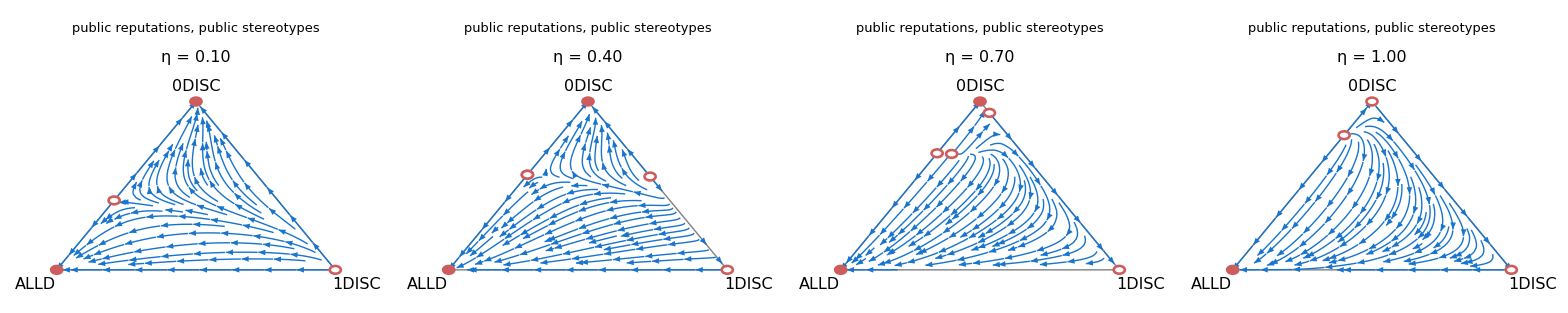

Fig4_E-H.pdf

```mathematica
(*Vary η/α, public/public*)
AAA=2;BBB=2;bb=3; rr1=1; rr2=0;
alphas={.1,.4,.7,1.};
stereotypes=Grid[Table[MakeTernaryPlot2[bb,1,AAA,BBB,0,1,alpha,rr1,rr2],{dummy, {0.}},{alpha,alphas}]]

filename="Fig4_E-H.pdf"
Export[directory<>filename,stereotypes];
Beep[] (* this figure takes a while; Beep[] will let you know when it's done *)
```

processing rep cost (η) = 0.1

processing rep cost (η) = 0.4

processing rep cost (η) = 0.7

processing rep cost (η) = 1.

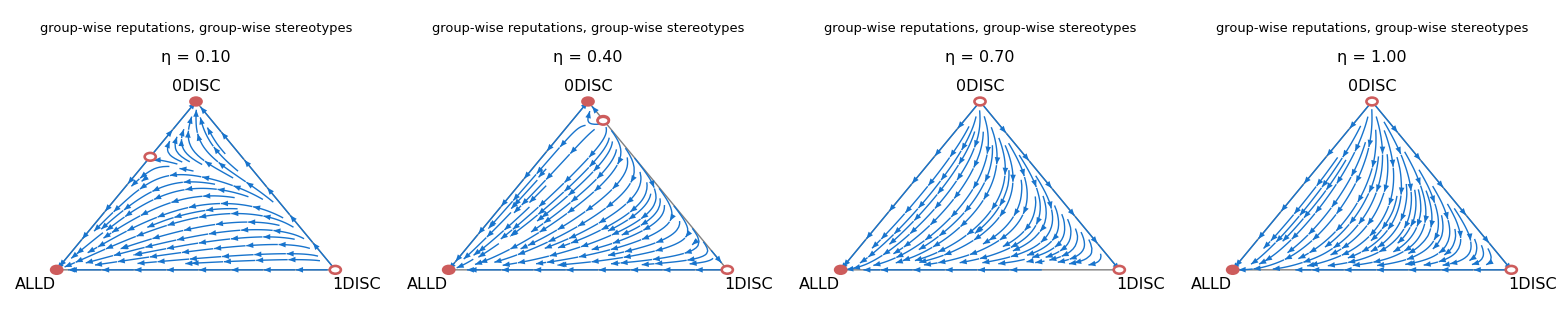

FigS11_E-H.pdf

```mathematica
(*Vary η/α, group-wise/group-wise*)
AAA=1;BBB=1;bb=3; rr1=1; rr2=0;
alphas={.1,.4,.7,1.};
stereotypes=Grid[Table[MakeTernaryPlot2[bb,1,AAA,BBB,0,1,alpha,rr1,rr2],{dummy, {0.}},{alpha,alphas}]]

filename="FigS11_E-H.pdf"
Export[directory<>filename,stereotypes];
Beep[] (* this figure takes a while; Beep[] will let you know when it's done *)
```